```mathematica
(*Coefficients*)
g=1.5;
κ=0.2;
(*Domain and spacing for calculating eigenfunctions*)
L=100;
dx=0.01;
(*total number of eigenfunctions to calculate.  To calculate the results in this paper you need at least enough such that there exists an ωk=2*ωb*)
total=200;
```

InterpolatingFunction::dmval: Input value {1.66752×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.66939×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.67127×10^-73} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

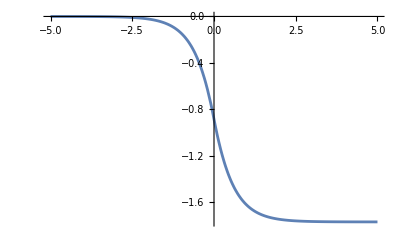

```mathematica
(*Loading in steady state soliton*)
Get["/scratch/network/zz3250/Wolfram Mathematica/SG_SS_Kappa0p2G1p5_N50000"]; (*put your own path here*)
(*Note that steady-state soliton depends on g,κ*)
PhiVSYKappa0p2G1p5=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss[x_]:=PhiVSYKappa0p2G1p5[(π^(1/2)*Exp[(2 π*κ)^(1/2) x])/(1+Exp[(2 π*κ)^(1/2) x])];data=Table[{x,ϕss[x]},{x,-150,150,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
Plot[ϕss[x],{x,-5,5}]
```

```mathematica
(*Generating eigenfunctions*)
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.8}];
```

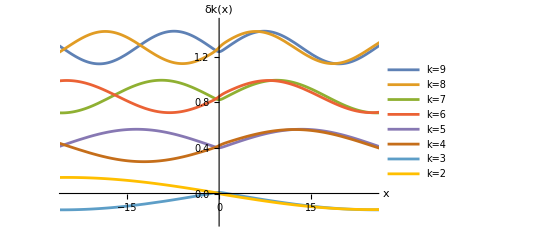

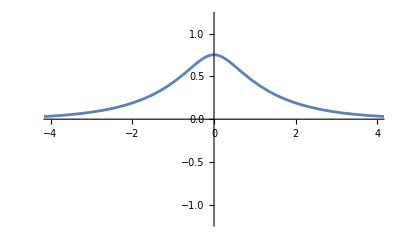

```mathematica
(*Plotting eigenfunctions*)
Plot[{Evaluate[fns[[9]]+1.28],Evaluate[fns[[8]]+1.28],Evaluate[fns[[7]]+.85],Evaluate[fns[[6]]+.85],Evaluate[fns[[5]]+.42],Evaluate[fns[[4]]+.42],Evaluate[fns[[3]]],Evaluate[fns[[2]]]},{x,-150,150},PlotRange->{{-25,25},{-.25,1.5}},AxesLabel->{"x","δk(x)"},PlotLegends->{"k=9","k=8","k=7","k=6","k=5","k=4","k=3","k=2"}]
Plot[Evaluate[fns[[1]]],{x,-5,5},PlotRange->{{-4,4},{-1.2,1.2}}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.392179}. NIntegrate obtained 0.-2.417×10^-8 ⅈ and 4.55747×10^-8 for the integral and error estimates.

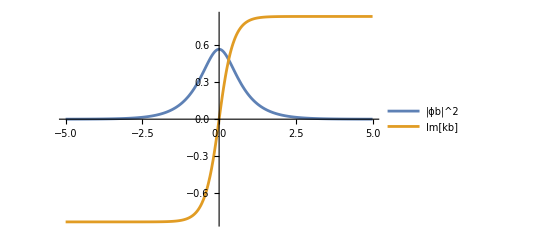

βb = -2.417×10^-8+0. ⅈ

```mathematica
(*Showing βb -> 0*)
efuns={};
For[i=1,i<=total,i++,
ψ=fns[[i]];
xRange=Range[-L/2,L/2,0.01];
originalData=Table[{x,ψ/. x->x},{x,xRange}];
originalInterp=Interpolation[originalData];
AppendTo[efuns,originalInterp];
];
ϕb[x_]:=efuns[[1]][x];
dϕb[x_]:=D[ϕb[X],X]/.X->x;
kb[x_]:=-I*dϕb[x]/ϕb[x];
βb=-I*NIntegrate[kb[x]*Abs[ϕb[x]]^2,{x,-L/2,L/2}];
Plot[{Abs[ϕb[x]]^2,Im[kb[x]]},{x,-5,5},PlotLegends->{"|ϕb|^2","Im[kb]"}]
Print["βb = ",βb]
```

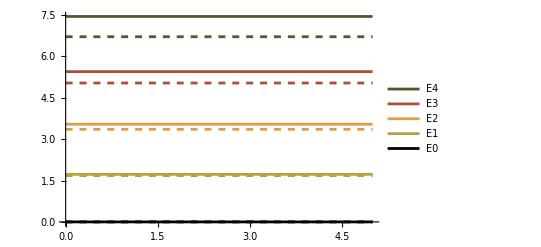

```mathematica
(*Plotting Lamb shift due to bound occupation*)
Vbbbb=NIntegrate[cosTerm[x]*fns[[1]]^4,{x,-L/2,L/2}];
ωb=Sqrt[vals[[1]]];
λ4=4*Pi*Pi/3;
nshift=(3*κ*λ4/(4*ωb^2))*Vbbbb;
Equad[n_]:=n*ωb;
Eshift[n_]:=n*ωb-n^2*nshift;
Plot[{Eshift[4],Equad[4],Eshift[3],Equad[3],Eshift[2],Equad[2],Eshift[1],Equad[1],Eshift[0],Equad[0]},{x,0,5},PlotStyle->{ColorData["SandyTerrain"][1],{ColorData["SandyTerrain"][1],Dashed},ColorData["SandyTerrain"][0],{ColorData["SandyTerrain"][0],Dashed},ColorData["SandyTerrain"][.25],{ColorData["SandyTerrain"][.25],Dashed},ColorData["SandyTerrain"][.75],{ColorData["SandyTerrain"][.75],Dashed},Black,{Black,Dashed}},PlotLegends->{"E4",None,"E3",None,"E2",None,"E1",None,"E0",None}]
```

```mathematica
(*Checking what the k2b mode is*)
Sqrt[vals[[88]]]
2*Sqrt[vals[[1]]]
```

3.33609

3.35569

```mathematica
(*Plotting Lamb shift due to k2b occupation*)
k=88; (*Put whatever k corresponds to the k2b mode here, even*)
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
ϕk=(1/Sqrt[2])*(fns[[k+1]]+I*fns[[k]]);
Vbbkstark=NIntegrate[cosTerm[x]*fns[[1]]^2*Abs[ϕk]^2,{x,-L/2,L/2}];
Eshiftk[n_,m_]:=n*ωb-(3*n*κ*λ4/(2*ωb))*(Vbbbb*n/(2*ωb)+Vbbkstark*m/(L*k2b)); (*n is bound occupation, m is k occupation*)
Plot[{Eshiftk[1,5],Eshiftk[1,4],Eshiftk[1,3],Eshiftk[1,2],Eshiftk[1,1],Eshiftk[1,0]},{x,0,5},PlotLabels->{"nb=1,nk=5","nb=1,nk=4","nb=1,nk=3","nb=1,nk=2","nb=1,nk=1","nb=1,nk=0"},PlotRange->All]
```

-Graphics-

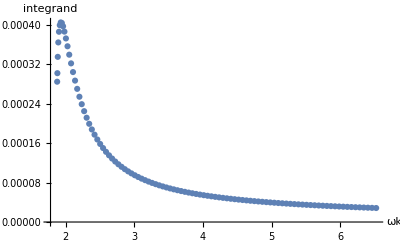

```mathematica
(*Showing integrand decays*)
klist={};
integrandlist={};
For[k=3,k<=total,k=k+2,
integrand=0;
ϕk=(1/Sqrt[2])*(fns[[k+1]]+I*fns[[k]]);
ωk=Sqrt[vals[[k]]];
Vbbkstark=NIntegrate[cosTerm[x]*fns[[1]]^2*Abs[ϕk]^2,{x,-L/2,L/2}];
ktilde=Sqrt[ωk^2-2*Pi*κ-g^2];
coeff=3*λ4/(ktilde*2*ωb*L);
integrand=coeff*Vbbkstark;
AppendTo[klist,k];
AppendTo[integrandlist,integrand];];
ListPlot[Transpose[{Sqrt[vals[[klist]]],Abs[integrandlist]}],AxesLabel->{"ωk","integrand"},PlotRange->All]
```

0.-0.229574 ⅈ

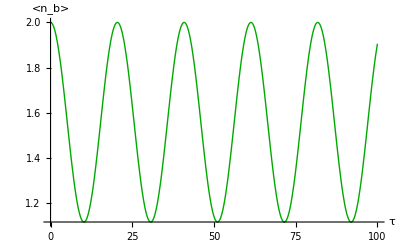

```mathematica
(*Rabi Oscillations*)
k=89;(*Put whatever k corresponds to the k2b mode, even*)
λ3=2*Pi^(3/2);
k2b=Sqrt[(2*ωb)^2-g^2-2*Pi*κ];
fk[x_]:=(fns[[k+1]]+I*fns[[k]])/Sqrt[2];
Vbbk=NIntegrate[Sin[intermediatePhi[x]]*fns[[1]]*fns[[1]]*fk[x],{x,-L/2,L/2}];
Bparam=λ3^2*Abs[Vbbk]^2/(4*ωb^3);
Cparam=3*I*λ4*Vbbbb/(4*ωb^2)
tMax=100;
sol=NDSolve[{nb'[t]==-2*Bparam*Re[s[t]],s'[t]==q[t]-Bparam*p[t]+Cparam*s[t],q'[t]==-2*Bparam*Re[s[t]],p'[t]==2*Re[s[t]],nb[0]==2,s[0]==0+0*I,q[0]==2,p[0]==0},{nb,s,q,p},{t,0,tMax}];
Plot[nb[t]/.sol,{t,0,tMax},AxesLabel->{Style["τ",14],Style["<n_b>",14]},PlotStyle->Directive[Darker@Green,Thick]]
```